```mathematica
(****
TEMPLATE FOR ITERATIVE OPTIMIZATION ALGORITHMS
Zicheng Gao
 ****)
```

```mathematica
(*** Iteration Settings ***)
InitIterationSettings[]:=(
(* Controls - zero fps means that there is NO DELAY *)
doPrint=False;
doPoint=True;
doGraph=False;
doEPlot=True;

showMistakes=False;
fps=0;

(* Tracker values *)
historyAmt=300;
);
InitIterationSettings[];
```

```mathematica
InitFunctionData[paramVariance_,manualTrueParams_,noiseFactor_, noiseDistribution_,forceData_,arbitfunc_]:=(
Clear[eFunc,gFunc,params];
ParamVariance=paramVariance;

(*If we are forcing data, use data, otherwise generate data*)
If[Length[forceData]>0,
Data=forceData;
DataLength=Length[Data];
SamplingSet=N@Range@DataLength/N@SamplingRate;
(* Else *),
SamplingSet=N@Range@DataLength/N@SamplingRate;
TrueParams=If[Length[manualTrueParams]>0,manualTrueParams,RandomReal[{-paramVariance,paramVariance},varamt]];
(* Data Generation *)
NoiselessData=((Fitfunction@@ #&)/@(Prepend[TrueParams, #]& /@SamplingSet));
AddNoise=(#+noiseFactor*RandomVariate[noiseDistribution])&;
Data=AddNoise/@NoiselessData;
];
(*Prep gradient*)
params=Table[Unique["p"],{varamt}];paramh=Hold@@params;

(* Objective and Gradient functions if there is no arbitrary minimizing function, of course *)
doArbitraryFitting=(arbitfunc=!={});
If[doArbitraryFitting,
eFunc=N@arbitfunc,
eFunc=paramh/._[vars__]:>Function[{vars},N[Mean[(((Fitfunction@@Prepend[{vars},#])&/@SamplingSet)-Data)^2]]]];
gFunc=paramh/._[vars__]:>Function[{vars},Evaluate@Grad[eFunc@@params,params]];
);
(*** Global Iteration Reset / Initialize ***)
InitIterationData[factorx_,manualParams_]:=(
totalIter=0;
factor=factorx;

(*History*)
iterParams=initParams=If[Length[manualParams]>0,manualParams,RandomReal[{-ParamVariance,ParamVariance},varamt]];
debugParams={iterParams};
err=eFunc@@iterParams;
prevErr=err+1.;

dir=gFunc@@iterParams;
debugErr={err};
doPerturb=False;
AError=(Total[(((Fitfunction@@Prepend[iterParams,#])&/@SamplingSet)-Data)^2]/(DataLength-varamt))^0.5;
);
LinePlot[points_, size_,amount_]:=Show[ListPointPlot3D[{If[amount>0&&size>amount,points[[-amount;;-1]],points]},PlotRange->All,ImageSize->Medium],Graphics3D@Line@points];
ReportIteration[i_]:=If[Mod[i,100]==0 && doPrint,Print["next dir:",dir,"\nerr:",err,"\nparams:",iterParams,"\niteration:",i];];
Visualize[]:=
Dynamic@Grid[{
{"Data vs Function","Parameter Space","Error over iterations"},
{If[doArbitraryFitting,"Arbitrary Optimization",ListPlot[{(Fitfunction@@Prepend[iterParams,#])&/@SamplingSet,Data},Joined->True,ImageSize->Medium,PlotLegends->None]],
If[doPoint,If[varamt==3,LinePlot[debugParams,totalIter,historyAmt],"Incorrect dimensionality"],"Disabled"],
If[doEPlot,ListLogLogPlot[debugErr,ImageSize->Medium,PlotRange->All],"Disabled"]},
{"Parameters, dir, Delta","Iterations, factor, corrections"},
{Column[{iterParams,factor*dir,factor*cdir}],
Column[{{totalIter,factor}}],
{AError,prevErr}}
},Frame->All,ItemSize->30];
RefineFactor[]:=(factor*=RefineRatio^AccelRefine;ConsecRefines++;TotalRefines++;AccelRefine+=AccelAmt;AccelBoost=1.;);
BoostFactor[]:=(factor*=BoostRatio^AccelBoost;prevErr=err;ConsecRefines=0;AccelBoost+=AccelAmt;AccelRefine=1.;);
AddToHistory[]:=(debugParams=Append[debugParams,iterParams];debugErr=Append[debugErr,err];);
ToSpacedString=Function[str,StringDrop[StringJoin@@((ToString[#]<>" ")&/@str),-1]];

(*Golden Ratio Search*)
Default[GoldenRatioSearch,7]=False;
Default[GoldenRatioSearch,8]=0;
GoldenRatioSearch[coeff_,init_,d_,surface_,tolerance_,min_,verbose_.,max_.]:=Module[{
gr=N@GoldenRatio,
f=coeff,l=coeff-LSTemp,h=coeff+N@GoldenRatio*LSTemp,g=coeff+N@GoldenRatio*LSTemp-LSTemp,
e=surface@@(init+#*d)&,i=0,
goLeft,goRight,trials=If[verbose,{}]},
goLeft[]:=(l-=gr*(h-l););
goRight[]:=(h+=(h-l)*gr;);
While[Abs[f-g]>tolerance&&(max==0||(max≠0&&i++<max)),
If[verbose,trials=Append[trials,{l,f,g,h}]];
If[e@f>min&&e@g>min,
If[e@h>e@l,(* Middles are above min error... but check to make sure that  *)
goLeft[];,
goRight[];
];,
If[e@h<e@f&&e@h<e@g,
goRight[];,(* Imbalanced *)
If[e@l<e@f&&e@l<e@g,
goLeft[];,
If[surface@@(init+d*f)<surface@@(init+d*g),h=g,l=f];(* No Problems *)
];];];
f=h-(h-l)/gr;g=l+(h-l)/gr;
];
If[verbose,Return@trials,Return@f];
];
BackLineSearch[coeff_,init_,d_,surface_,tolerance_,min_,boost_,refine_]:=Module[
{a=coeff*boost,
e=surface@@(init+#*d)&},
While[e@a>min,
a*=refine];
Return@a
];

ConjFormula[curr_,prev_]:=Dot[curr,N@(curr-prev)]/N@Dot[prev,prev];
Iterate[n_,tolerance_,min_]:=(
i=0;
(* First Iteration *)
dir=-gFunc@@iterParams;
err=eFunc@@iterParams;
factor=GoldenRatioSearch[factor,iterParams,dir,eFunc,LSTol,err];
iterParams+=factor*dir;
cdir=prevdir=dir;
(* Successive Iteration *)
While[(i<n &&(NoErr||AError>tolerance&&Norm@dir>min)),
If[doPerturb,iterParams+=Normalize[RandomReal[1.,varamt]]/dir.dir];
dir=-gFunc@@iterParams;
err=eFunc@@iterParams;
cdir=dir+Max[0,ConjFormula[dir,prevdir]]*cdir;
factor=GoldenRatioSearch[factor,iterParams,cdir,eFunc,LSTol,err];
iterParams+=factor*cdir;
AError=(Total[(((Fitfunction@@Prepend[iterParams,#])&/@SamplingSet)-Data)^2]/(DataLength-varamt))^0.5;
i++;totalIter++;AddToHistory[];If[fps≠0&&ConsecRefines==0,Pause[fps];];
]);

HDFD[index_]:=Abs@Fourier[Data*Exp[2I π(index-2)N@(Range@DataLength-1)/DataLength],FourierParameters->{0,2/DataLength}];
FindMax[list_]:=Position[list,Max@list][[1,1]];
FindIndexFreq[index_]:=N@((#-2+2(FindMax@HDFD@#-1)/DataLength)*2π*SamplingRate/DataLength)&/@index;
RecoverIndices[]:=First/@(Take[#,Round[(Length@#)/2.]]&@FindPeaks@Abs@Fourier@Data);
RecoverFreqList[]:=(Select[RecoverIndices[],#>0&]//FindIndexFreq);
RecoverDataFreq[i_]:=If[i≤Length@#,#[[i]],#[[Length@#]]]&@RecoverFreqList[];
```

```mathematica
RecordedComparisonData={};
```

```mathematica
(* SET DATA *)
varamt=3;
DataLength=100;
SamplingRate=100;
Fitfunction=Sin[30*#1*#2+#4] Exp[-#1*#3]&;
InitFunctionData[5.,{-1.8843439074598045,1.7127700566735733,-2.92633344958303},0.2,NormalDistribution[1,0.25],{},{}];
TrueParams
```

{-1.88434,1.71277,-2.92633}

```mathematica
(* BEGIN ITERATION *)
InitIterationSettings[];
Smoothness=5;
showMistakes=False;

Balance=1.01;
Impatience=1.18;
BoostRatio=(Balance*Impatience)^0.5;
RefineRatio=(Balance/Impatience)^0.5;
ErrorRatio=1.;

SmoothingFunction[l_]:=Total[MapIndexed[#1 /2.^First[#2]&,l]]/Smoothness;
InitIterationData[0.01,{RecoverDataFreq[2]/30,1,0}];
doPerturb=False;
Column[{
Visualize[],
ToSpacedString@{"Balance: ",Balance=RefineRatio*BoostRatio},
ToSpacedString@{"Impatience: ",Impatience=BoostRatio/RefineRatio},
ToSpacedString@{"Frequency indices: ", RecoverIndices[]},
ToSpacedString@{"Data frequencies: ", RecoverFreqList[]},
ToSpacedString@{"TrueParams",TrueParams}
}]
```

Balance:  1.01
Impatience:  1.18
Frequency indices:  {1, 10, 22, 27, 30, 35, 42, 47, 50}
Data frequencies:  {0., 56.2973, 135.214, 163.614, 179.322, 213.503, 259.747, 290.032, 305.111}
TrueParams {-1.88434, 1.71277, -2.92633}

```mathematica
(*** Iteration loop ***)
NoErr=False;
LSTemp=0.5;
LSTol=0.001;
ITol=0.001;
fps=1./60.;
Iterate[1,ITol,10.^-7]
```

General::unfl: Underflow occurred in computation.

General::stop: Further output of General :: unfl will be suppressed during this calculation.

$Aborted

```mathematica
(** Data Recording **)
RecordedComparisonData=Catenate[{RecordedComparisonData,
{{{"Smoothness",Smoothness},
debugErr,debugParams,TotalRefines,
{"Balance",Balance},{"Impatience",Impatience},{"Iterations",totalIter}}}}];
```

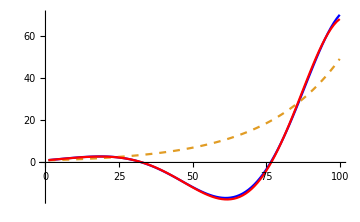

-Graphics3D-

```mathematica
(***Diagnostic Tools***)

(*Parameter History*)
Grid[debugParams[[-10;;-1]]];
Column[eFunc @@ #&/@ debugParams[[-10;;-1]]];
Grid[gFunc @@ #&/@ debugParams[[-10;;-1]]];

(*"Best Parameters" Generated with NMinimize*)
AutoParams=params/.NMinimize[eFunc @@ params,params][[2]];

(*Compare current data, auto-fitted data, and generated data*)
ListPlot[{
(Fitfunction@@Prepend[iterParams,#])&/@SamplingSet,
(Fitfunction@@Prepend[AutoParams,#])&/@SamplingSet,
Data},
Joined->True,ImageSize->Medium,PlotStyle->{Blue,Dashed,Red}]
LinePlot[debugParams,Length@debugParams,Length@debugParams]
```

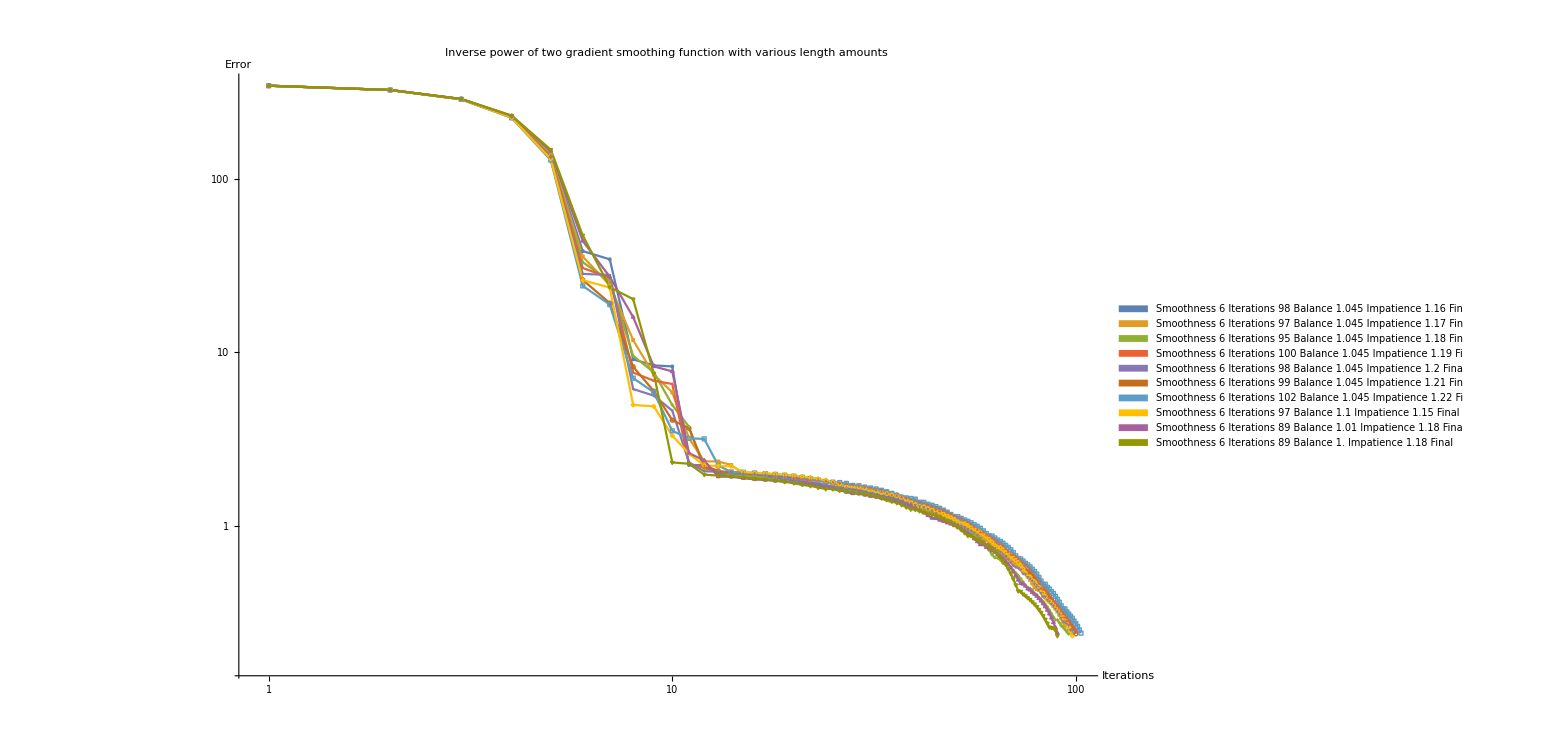

```mathematica
ListLogLogPlot[
Table[RecordedComparisonData[[sm,2]],{sm,1,Length@RecordedComparisonData}],PlotLegends->SwatchLegend[
Table[
Column[
Join[
Flatten@ToSpacedString/@RecordedComparisonData[[sm,{1,7,5,6}]],
{ToSpacedString@{"Final error:",Last@RecordedComparisonData[[sm,2]]},
ToSpacedString@{"Corrections:",RecordedComparisonData[[sm,4]]}}
]
],{sm,1,Length@RecordedComparisonData}],
LegendFunction->"Panel",
LegendLayout->"Row"],
PlotLabel->"Inverse power of two gradient smoothing function with various length amounts",
AxesLabel->{"Iterations","Error"},
PlotRange->All,
ImageSize->1200,
Joined->True,
PlotMarkers->{Automatic,4}]
```

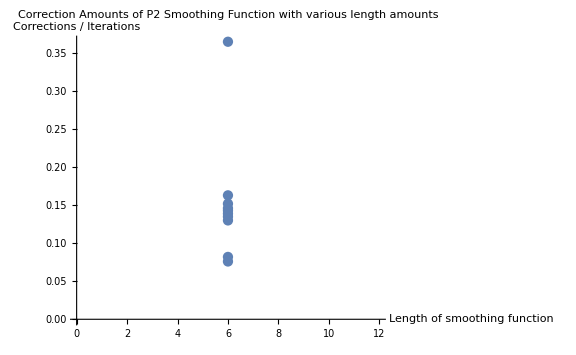

```mathematica
ListPlot[
Table[{RecordedComparisonData[[sm,1,2]],RecordedComparisonData[[sm,4]]/1000.},{sm,1,Length@RecordedComparisonData}],
AxesLabel->{"Length of smoothing function","Corrections / Iterations"},
PlotLabel->"Correction Amounts of P2 Smoothing Function with various length amounts",
ImageSize->Large
]
```

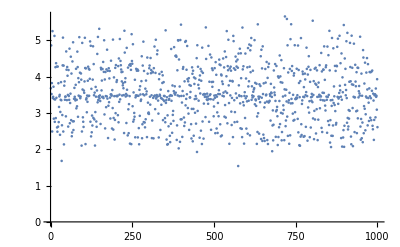

```mathematica
timings={};
Do[timings=Append[timings,First@(gFunc@@iterParams//AbsoluteTiming)/First@(eFunc@@iterParams//AbsoluteTiming)],{1000}]
ListPlot@timings
```

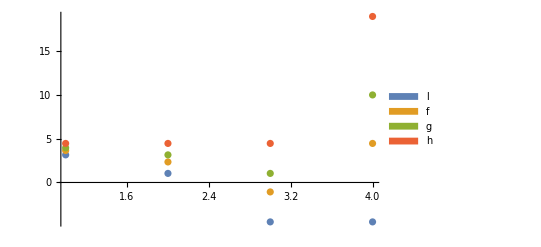

0.0528241

```mathematica
GRSR=GoldenRatioSearch[factor,iterParams,cdir,eFunc,LSTol,err,True,4];
ListPlot[Transpose@GRSR,PlotLegends->SwatchLegend[{l,f,g,h}],PlotRange->All]
EFC=eFunc@@(iterParams+#*cdir)&;
err
Manipulate[Show[
ListPlot[Map[{#,EFC@#}&,GRSR,{2}]⟦i;;i+1⟧,PlotStyle->{PointSize@Small,PointSize@Large}],
Plot[err,{i,-10,10}]
],{i,1,Length@GRSR-1,1},ContinuousAction->False]
```